# GRADOS EN INGENIERÍA TELEMÁTICA E INGENIERÍA DE TECNOLOGÍAS DE TELECOMUNICACIÓN Métodos Matemáticos de las Telecomunicaciones (curso 23 - 24) Practica 3 (2 de 3). Series funcionales. Series de potencias.

## Series funcionales

El proceso para sumar infinitas funciones f_1(x)+f_2(x)+f_3(x)+...+f_n(x)+... es análogo al realizado para sumar infinitos números. Es decir, se van realizando sumas parciales:

s_n(x)=f_1(x)+f_2(x)+f_3(x)+...+f_n(x)

y la función suma f(x)=∑_(n=1)^∞ f_n(x) es el límite de las sumas parciales:

f(x)=∑_(n=1)^∞ f_n(x)=lim_(n→∞) s_n(x)
para los puntos x donde exista este límite

Al conjunto de puntos x donde existe lim_(n→∞) s_n(x) se llama campo de convergencia de la serie funcional.

## Ejercicio 1

Sea la serie funcional ∑_(n=1)^∞ x^2/((1+x^2)^n)=x^2/(1+x^2)+x^2/((1+x^2)^2)+x^2/((1+x^2)^3)+...+x^2/((1+x^2)^n)+... Dibujar sobre unos mismos ejes la suma parcial de orden 3 s_3(x), la suma parcial de orden 5 s_5(x) y la suma parcial de orden 10 s_10(x). En función de las gráficas deducir la suma de esta serie funcional.

1. Suma parcial de orden 3

```mathematica
s3[x_] = ∑_(n=1)^3 x^2/((1 + x^2)^n)
```

x^2/((1+x^2)^3)+x^2/((1+x^2)^2)+x^2/(1+x^2)

2. Suma parcial de orden 5

```mathematica
s5[x_] = ∑_(n=1)^5 x^2/((1 + x^2)^n)
```

x^2/((1+x^2)^5)+x^2/((1+x^2)^4)+x^2/((1+x^2)^3)+x^2/((1+x^2)^2)+x^2/(1+x^2)

3. Suma parcial de orden 10

```mathematica
s10[x_] = ∑_(n=1)^10 x^2/((1 + x^2)^n)
```

x^2/((1+x^2)^10)+x^2/((1+x^2)^9)+x^2/((1+x^2)^8)+x^2/((1+x^2)^7)+x^2/((1+x^2)^6)+x^2/((1+x^2)^5)+x^2/((1+x^2)^4)+x^2/((1+x^2)^3)+x^2/((1+x^2)^2)+x^2/(1+x^2)

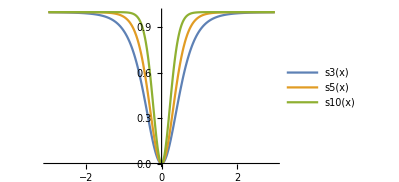

```mathematica
Plot[{s3[x], s5[x], s10[x]}, {x, -3, 3}, PlotRange-> All, PlotLegends-> "Expressions"]
```

Se observa que la serie ∑_(n=1)^∞ x^2/((1+x^2)^n) = f(x) siendo f(x) = Piecewise[{{1, si x≠ 0}, {0, si x= 0}}]

## Ejercicio 2

Sea la serie funcional x+x^2/(2!)+x^3/(3!)+x^4/(4!)+...=∑_(n=1)^∞ x^n/(n!) Dibujar sobre unos mismos ejes la suma parcial de orden 5 s_5(x), la suma parcial de orden 8 s_8(x) y la función f(x)=ⅇ^x-1. En función de las gráficas deducir la suma de esta serie funcional.

1.Suma parcial de orden 5

```mathematica
s5[x_] := ∑_(n=1)^5 x^n/(n!)
```

2. Suma parcial de orden 8

```mathematica
s8[x_] := ∑_(n=1)^8 x^n/(n!)
```

```mathematica
f[x_] := E^x - 1
```

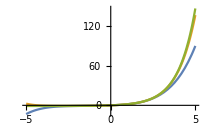

```mathematica
Plot[{s5[x], s8[x], f[x]}, {x, -5, 5}, PlotRange -> All, PlotLegends -> "Expressions"]
```

Parece evidente que ∑_(n=1)^∞ x^n/(n!) = ⅇ^x - 1. Comprobemos esto con Mathematica:

```mathematica
∑_(n=1)^∞ x^n/(n!)
```

-1+ⅇ^x

## Convergencia uniforme

La convergencia puntual de series funcionales, aunque conceptualmente es sencilla, algunas veces puede producir resultados aparentemente extraños.

Por ejemplo, en el ejercicio 1, vimos que las sumas parciales de la serie ∑_(n=1)^∞ x^2/((1+x^2)^n) eran funciones continuas, sin embargo, su suma era una función discontinua: f(x)=Piecewise[{{1, si x≠0}, {0, si x=0}}]

En cambio, en el ejercicio 2, vimos que las sumas parciales de la serie ∑_(n=1)^∞ x^n/(n!) que también son funciones continuas, su suma sí es una función continua. Además, se puede probar que la función suma f(x)=ⅇ^x-1 hereda muchas propiedades de las funciones que componen la suma.

Esto ocurre porque, en el ejercicio 2, la convergencia en dicho intervalo es uniforme, que es algo más que la convergencia puntual.

Definición. La serie de funciones ∑_(n=1)^∞ f_n(x) converge uniformemente en C hacia una función f(x) si dado un ε existe un m∈ℕ, que depende de ε pero no de x, tal que para todo n>m:

|s_n(x)-f(x)|<ε

Gráficamente, la convergencia uniforme equivale a decir que dado una franja alrededor de la función suma f(x):

f(x)-ε y f(x)+ε

a partir de un término en delante toda suma parcial s_n(x) cae dentro de dicha franja:

-Graphics-

Entre los distintos teoremas que nos permite asegurar la convergencia uniforme de una serie de funciones, el más sencillo, y utilizado, es el criterio de Weierstrass que consiste en encontrar una serie numérica convergente que a su vez mayora a la serie de funciones.

## Ejercicio 3

Demostrar que la serie la serie funcional 1+x+x^2+x^3+x^4+... tiene convergencia uniforme en el intervalo [0,0.5]

## Definición de serie de potencias

Se define la serie de potencias centrada en el punto x_0 a la serie funcional que tiene la siguiente forma:

a_0+(a_1(x-x_0))^1+(a_2(x-x_0))^2+...+(a_n(x-x_0))^n+...=∑_(n=0)^∞ (a_n(x-x_0))^n

donde a_n son números y se llaman coeficientes de la serie de potencias.

Nota. Si la serie de potencias está centrada en el punto 0, su aspecto sería:

a_0+a_1 x^1+a_2 x^2+a_3 x^3+...+a_n x^n+...=∑_(n=0)^∞ a_n x^n

## Radio de convergencia de la serie de potencias

Teorema. Sea la serie de potencias ∑_(n=0)^∞ (a_n(x-x_0))^n, convergerá a la función f(x) en el intervalo (x_0-R,x_0+R) donde R se llama radio de convergencia y se calcula mediante la siguiente fórmula:

R=1/(lim_(n→∞) (|a_(n+1)|)/(|a_n|))

Nota 1. Si lim_(n→∞) (|a_(n+1)|)/(|a_n|)=0 la convergencia de la serie de potencias será todo ℝ. 
Nota 2. Si lim_(n→∞) (|a_(n+1)|)/(|a_n|)=∞ la convergencia se reduce al punto x_0.
Nota 3. En los extremos del intervalo de convergencia, la serie de potencias puede ser convergente o no. Así, el campo de convergencia será uno de los siguientes intervalos:

(x_0-R,x_0+R),  [x_0-R,x_0+R),  (x_0-R,x_0+R],  [x_0-R,x_0+R]

## Ejercicio 4

Calcular el campo de convergencia de la serie de potencias ∑_(n=0)^∞ x^n/(n!)

∑_(n=0)^∞ x^n/(n!)=∑_(n=0)^∞ 1/(n!)x^n, luego los coeficientes de esta serie de potencias son: a_n=1/(n!)

## Ejercicio 5

Calcular el campo de convergencia de la serie de potencias ∑_(n=1)^∞ ((-1)^(n+1)(x-5)^n)/(n 5^n)

## Ejercicio 6

Calcular el radio de convergencia de la serie: ∑_(n=1)^∞ n^3/4^n x^(2n+1)

■

Pongamos ∑_(n=1)^∞ n^3/4^n x^(2n+1) como una serie de potencias de la forma ∑_^ a_n x^n.

∑_(n=1)^∞ n^3/4^n x^(2n+1)=x∑_(n=1)^∞ n^3/4^n x^(2n)=x∑_(n=1)^∞ n^3/4^n(x^2)^n

Haciendo el cambio de variable x^2=t:

∑_(n=1)^∞ n^3/4^n x^(2n+1)=x∑_(n=1)^∞ n^3/4^n t^n

## Desarrollo en series de potencias.

Aunque parezca extraño, el problema que tiene más utilidad no consiste en calcular la suma de una serie de potencias, sino el contrario. Dada una cierta función, se trata de calcular la serie de potencias que converja a dicha función en un determinado campo de convergencia.

Dada una función f(x) infinitamente derivable en un intervalo que contiene al punto x_0 casi siempre vamos a poder encontrar una serie de potencias:

a_0+(a_1(x-x_0))^1+(a_2(x-x_0))^2+...+(a_n(x-x_0))^n+...=∑_(n=0)^∞ (a_n(x-x_0))^n

La suma parcial de orden n del desarrollo en serie de potencias de la función f(x) va a coincidir con el polinomio de Taylor de orden n de la función f(x).

## Ejercicio 7

Calcular la serie de potencias y el radio de convergencia de la función x ln (x+1)

■

Vamos a desarrollar la función ln x para ello vamos a obtener el polinomio de Taylor de orden 5 y vemos si es fácil seguir un patrón para calcular la derivada enésima.

## Propiedades de las series de potencias.

1) La función suma de la serie de potencias f(x)=∑_(n=0)^∞ a_n x^n es continua en todo el campo de convergencia.

2) La función suma de la serie de potencias f(x)=∑_(n=0)^∞ a_n x^n es derivable en el intervalo (-R,R) y su derivada es:

f' (x) = ∑_(n=1)^∞ n a_n x^(n-1)

Es decir, la derivada de una serie de potencias se obtiene derivando cada sumando.

3) La función suma de la serie de potencias f(x)=∑_(n=0)^∞ a_n x^n es integrable en todo intervalo de la forma [a,b] incluido en el campo de convergencia. Además, la integración se puede realizar término a término:

∫_a^b f(x)ⅆx = ∑_(n=0)^∞ (a_n [x^(n+1)/(n+1)])_a^b

## Ejercicio 8

A partir de la serie funcional 1-x+x^2-x^3+... Calcular el desarrollo en serie de potencias de 1/(1+x)^2

■

La serie funcional:

1-x+x^2-x^3+...=∑_(n=0)^∞ (-1)^n x^n

## Ejercicio 9

A partir de la serie funcional 1-x^2+x^4-x^6+... Calcular el desarrollo en serie de potencias de arctag x.